Importing your calibration films and Creating the dose calibration curves

Retrieve the file paths of the calibration files and then import the images.

```mathematica
Clear["Global`*"]
```

```mathematica
calFilePath=SystemDialogInput["FileOpen"]
```

/Users/cptfinch/Documents/maths/gafchromic/my cal and uniformity films/img001.tif

```mathematica
calFile=Import[calFilePath]
```

-Graphics-

The next step is to obtain the rectangular regions of interest from the imported images and to obtain a list of the regions in order of increasing dose. Incidentally for best practice the calibration strips should be scanned during one scan; in other words all of the calibration strips should be placed on the scanner bed and scanned together. This removes any variation in the scanner response over successive scans - removing the variability in response caused by inter-scan variability.   

To select the regions of interest use the following steps: Make the image below active by clicking on it; a number of options will appear along the bottom of image, select the rectangular select tool; drag over the irradiated regions in order to create selected central rectangular regions of the irradiated parts of each strip. 

Once all regions are selected, copy and paste the list to the right of calRoiList=

/Users/cptfinch/Documents/maths/gafchromic/my cal and uniformity films/img001.tif[First]

```mathematica
calRoiList={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} ;
```

The following ColorSeparate function returns an n by 4 matrix instead of an n by 3 matrix. In other words there are four columns where I would have expected three columns, three since that corresponds to the three colour channels. The fourth column seems to be simply blank, so I am not sure where it comes from.

```mathematica
rgbCalList=Map[ColorSeparate,calRoiList];
```

Obtain here lists containing the calibration regions for respective colour channels. They are obtained by extracting them from the rgbCalList.

```mathematica
redCalRois=rgbCalList[[All,1]];
```

```mathematica
greenCalRois=rgbCalList[[All,2]];
```

```mathematica
blueCalRois=rgbCalList[[All,3]];
```

A pure function f to obtain the mean value of a calibration region.

```mathematica
f[x_]:=Mean[Flatten[ImageData[x]]];
```

f is mapped over each calibration region to obtain a list of values corresponding to the mean pixel values of the calibration regions. Pixel values are normalized to 1. i.e. 0..65535 is mapped to 0..1

```mathematica
redCal=Map[f,redCalRois];
```

```mathematica
blueCal=Map[f,blueCalRois];
```

```mathematica
greenCal=Map[f,greenCalRois];
```

Sort the values in order corresonding from high pixel value to low pixel value. This corresponds to the order of low dose to high dose.

```mathematica
redCalPixelValueLowToHighDose=Sort[redCal,Greater];
```

```mathematica
blueCalPixelValueLowToHighDose=Sort[blueCal,Greater];
```

```mathematica
greenCalPixelValueLowToHighDose=Sort[greenCal,Greater];
```

Input the doses given to the calibration strips in the order low to high dose. Here I have specified dose in Gy. Be sure to keep it in this format - each number separated by a comma and curly braces at each end.

```mathematica
cal1Doses={0,1/2,1,2,4,7,9};
```

```mathematica
redCalPoints=Transpose[{cal1Doses,redCalPixelValueLowToHighDose}];
blueCalPoints=Transpose[{cal1Doses,blueCalPixelValueLowToHighDose}];
greenCalPoints=Transpose[{cal1Doses,greenCalPixelValueLowToHighDose}];
```

```mathematica
redLine=FindFit[redCalPoints,(r+s*D)/(t+D),{r,s,t},D];
blueLine=FindFit[blueCalPoints,(r+s*D)/(t+D),{r,s,t},D];
greenLine=FindFit[greenCalPoints,(r+s*D)/(t+D),{r,s,t},D];
```

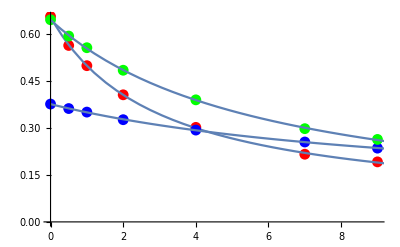

```mathematica
Show[ListPlot[redCalPoints, PlotStyle->Red],Plot[{(r+s*D)/(t+D)/.redLine}, {D, 0, 15}],
	ListPlot[blueCalPoints, PlotStyle->Blue], Plot[{(r+s*D)/(t+D)/.blueLine}, {D, 0, 15}],
	ListPlot[greenCalPoints, PlotStyle->Green],Plot[{(r+s*D)/(t+D)/.greenLine}, {D, 0, 15}]]
```

## Converting Application films to dose using the Multi-channel method

```mathematica
appFilmFilePath=SystemDialogInput["FileOpen"];
appFilm=Import[appFilmFilePath];
```

```mathematica
redChannel=ColorSeparate[appFilm,"R"];
blueChannel=ColorSeparate[appFilm,"G"];
greenChannel=ColorSeparate[appFilm,"B"];
```

```mathematica
redFit[dose_]=((r+s*dose)/(t+dose))/.redLine;
blueFit[dose_]=((r+s*dose)/(t+dose))/.blueLine;
greenFit[dose_]=((r+s*dose)/(t+dose))/.greenLine;
```

```mathematica
f[pixelR_,pixelB_,pixelG_]:=bestDose/.Last[Minimize[(pixelR-redFit[bestDose])^2+(pixelB-blueFit[bestDose])^2+(pixelG-greenFit[bestDose])^2,bestDose]];
```

```mathematica
ImageApply[f,{redChannel,blueChannel,greenChannel}]
```

The following is test data

```mathematica
croppedApp=ImageCrop[appFilm,{2,2}]
```

```mathematica
croppedFilm[width_,height_]:=ImageCrop[appFilm,{width,height}]
```

```mathematica
multichannelMethodNC[pixel_]:=bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose]];
```

```mathematica
multichannelMethod[pixel_]:=bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose<5 &&bestDose>2,bestDose]];
```

```mathematica
multichannelCompileNC=Compile[{pixel} ,bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose]]];
```

```mathematica
multichannelCompileLocal=Compile[{pixel} ,bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose]]];
```

```mathematica
multichannelFunctionLocal[pixel_]:=bestDose/.Last[FindMinimum[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,{bestDose,3.}]];
```

```mathematica
Timing[Map[multichannelMethodNC,ImageData[croppedApp],{2}]]
```

{0.43157,{{3.38007,3.41069},{3.37348,3.39505}}}

```mathematica
AbsoluteTiming[Map[multichannelMethodNC,ImageData[croppedApp],{2}]]
```

{0.41316,{{3.38007,3.41069},{3.37348,3.39505}}}

```mathematica
Timing[Map[multichannelMethod,ImageData[croppedApp],{2}]]
```

{0.56349,{{3.38007,3.41069},{3.37348,3.39505}}}

```mathematica
First[Timing[Map[multichannelMethodNC,ImageData[croppedFilm[4,4]],{2}]]]
```

1.70554

```mathematica
ListPlot[Table[First[Timing[Map[multichannelMethodNC,ImageData[croppedFilm[i,i]],{2}]]],{i,1,4}],AxesLabel->{n,t}]
```

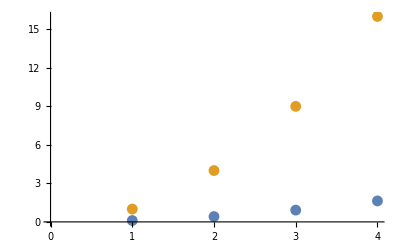

```mathematica
ListPlot[{Table[n^2,{n,1,4}],Table[First[Timing[Map[multichannelMethodNC,ImageData[croppedFilm[i,i]],{2}]]],{i,1,4}]}]
```

```mathematica
Table[n^2,{n,1,4}]
```

{1,4,9,16}

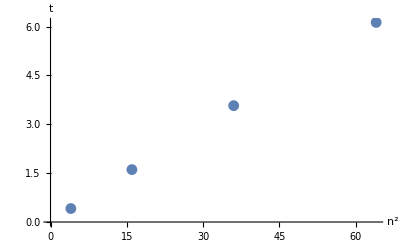

```mathematica
ListPlot[Transpose[{Table[(2n)^2,{n,1,4}],Table[First[Timing[Map[multichannelMethodNC,ImageData[croppedFilm[2i,2i]],{2}]]],{i,1,4}]}],AxesLabel->{n^2,t}]
```

```mathematica
Timing[Map[multichannelMethodNC,ImageData[croppedFilm[6,6]],{2}]]
```

{3.48488,{{3.34329,3.30762,3.32114,3.3511,3.33593,3.33377},{3.36737,3.36254,3.39144,3.39948,3.38116,3.37183},{3.37358,3.39661,3.38007,3.41069,3.39187,3.36742},{3.43893,3.4249,3.37348,3.39505,3.37584,3.35356},{3.45475,3.41494,3.40306,3.40544,3.36697,3.33743},{3.40577,3.39437,3.37157,3.38853,3.35627,3.34978}}}

```mathematica
Timing[Map[multichannelCompileNC,ImageData[croppedFilm[6,6]],{2}]]
```

CompiledFunction::cfsa: Argument {0.371237, 0.452125, 0.312459} at position 1 should be a "machine-size real number".

CompiledFunction::cfsa: Argument {0.371832, 0.45333, 0.314885} at position 1 should be a "machine-size real number".

CompiledFunction::cfsa: Argument {0.372015, 0.45333, 0.313359} at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

{3.73641,{{3.34329,3.30762,3.32114,3.3511,3.33593,3.33377},{3.36737,3.36254,3.39144,3.39948,3.38116,3.37183},{3.37358,3.39661,3.38007,3.41069,3.39187,3.36742},{3.43893,3.4249,3.37348,3.39505,3.37584,3.35356},{3.45475,3.41494,3.40306,3.40544,3.36697,3.33743},{3.40577,3.39437,3.37157,3.38853,3.35627,3.34978}}}

```mathematica
Dimensions[ImageData[appFilm]]
```

{685,544,3}

```mathematica
GaussianFilter[appFilm,2]
```

-Graphics-

```mathematica
Timing[Map[multichannelMethodNC,ImageData[croppedFilm[3,3]],{2}]]
```

{0.93831,{{3.39661,3.38007,3.41069},{3.4249,3.37348,3.39505},{3.41494,3.40306,3.40544}}}

```mathematica
Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[3,3]],{2}]]
```

{0.01941,{{3.39661,3.38007,3.41069},{3.4249,3.37348,3.39505},{3.41494,3.40306,3.40544}}}

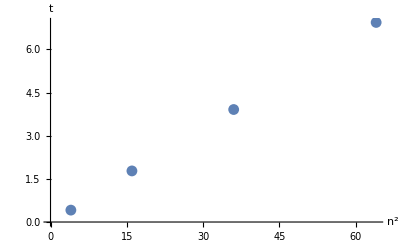

```mathematica
ListPlot[Transpose[{Table[(2n)^2,{n,1,4}],Table[First[Timing[Map[multichannelMethodNC,ImageData[croppedFilm[2i,2i]],{2}]]],{i,1,4}]}],AxesLabel->{n^2,t}]
```

```mathematica
ListPlot[Transpose[{Table[(2n)^2,{n,1,4}],Table[First[Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[2i,2i]],{2}]]],{i,1,5}]}],AxesLabel->{n^2,t}]
```

Transpose::nmtx: The first two levels of {{4, 16, 36, 64}, {0.00826, 0.0276, 0.05599, 0.095626, 0.15396}} cannot be transposed.

Transpose::nmtx: The first two levels of {{4., 16., 36., 64.}, {0.00826, 0.0276, 0.05599, 0.095626, 0.15396}} cannot be transposed.

Transpose::nmtx: The first two levels of {{4., 16., 36., 64.}, {0.008258, 0.027601, 0.055991, 0.095626, 0.153956}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{4., 16., 36., 64.}, {0.008258, 0.027601, 0.055991, 0.095626, 0.153956}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{4,16,36,64},{0.00826,0.0276,0.05599,0.095626,0.15396}}],AxesLabel→{n^2,t}]

```mathematica
Timing[Map[multichannelMethodNC,ImageData[croppedFilm[2,2]],{2}]]
```

{0.42376,{{3.38007,3.41069},{3.37348,3.39505}}}

```mathematica
Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[2,2]],{2}]]
```

{0.009751,{{3.38007,3.41069},{3.37348,3.39505}}}

```mathematica
Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[10,1]],{2}]]
```

{0.02056,{{3.37217,3.38121,3.43893,3.4249,3.37348,3.39505,3.37584,3.35356,3.36446,3.3795}}}

```mathematica
Dimensions[ImageData[appFilm]]
```

{685,544,3}

```mathematica
firstTwoFromList=Function[list,{list[[1]],list[[2]]}]
```

```mathematica
Times[Flatten[firstTwoFromList[Dimensions[ImageData[appFilm]]]]]
```

{685,544}

```mathematica
TimesFirstTwoInList=Function[listIn,listIn[[1]]*listIn[[2]]]
```

Function[listIn,listIn⟦1⟧ listIn⟦2⟧]

```mathematica
TimesFirstTwoInList[Dimensions[ImageData[appFilm]]]/10//N
```

37264.

```mathematica
37264.*First[Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[10,1]],{2}]]]
```

650.629

```mathematica
(651/60.)
```

10.85

```mathematica
caldImage=Timing[Map[multichannelFunctionLocal,ImageData[croppedFilm[200,200]],{2}]]
```

{54.88471,{{3.44275,3.46995,3.3874,3.37937,3.37483,3.37553,3.3539,3.35114,3.36296,182,3.42569,3.44517,3.47366,3.433,3.41651,3.45853,3.4542,3.47164,3.49406},198,{1}}}
 |  |  |  |

```mathematica
First[caldImage]
```

54.88471

```mathematica
caldImage=Timing[Map[multichannelFunctionLocal,ImageData[appFilm],{2}]]
```

{513.1907,{1}}
 |  |  |  |

```mathematica
Image[caldImage]
```

Image::imgarray: The specified argument {513.1907, {« 1 »}} should be an array of rank 2 or 3 with machine-sized numbers.

Image[{513.1907,{{3.88121,3.84585,4.02483,4.4216,4.2216,4.58524,4.99847,5.26942,5.47415,526,4.51268,4.54545,4.61844,4.62919,4.64552,4.62419,4.6197,4.64619,4.72708},683,{1}}}]
 |  |  |  |

```mathematica
caldImage[[2]]
```

{{3.88121,3.84585,4.02483,4.4216,4.2216,4.58524,4.99847,5.26942,5.47415,5.50783,5.73055,5.88888,5.85712,5.74261,5.76154,5.78043,5.73131,5.61423,5.62258,5.43534,5.54871,5.5716,5.42967,5.40366,5.39879,5.32723,5.27024,5.43868,5.50732,5.38956,5.43439,5.3748,5.44084,5.38121,5.36496,5.40096,5.37107,5.32275,5.27116,5.15027,5.11638,5.10772,5.11213,5.00837,5.02392,5.11364,5.27569,5.2412,5.46901,5.2131,444,4.07699,4.09191,4.06715,4.01041,3.96666,3.96862,3.92584,3.91017,3.94079,3.89271,4.40085,3.91139,3.8257,3.88745,3.95722,4.03488,3.993,3.99108,4.03747,4.1417,4.13382,4.07583,4.03265,4.00468,4.08292,4.07422,4.14394,4.15794,4.15967,4.18007,4.135,4.17544,4.2053,4.22129,4.30197,4.27771,4.1991,4.19077,4.23245,4.35417,4.47339,4.51268,4.54545,4.61844,4.62919,4.64552,4.62419,4.6197,4.64619,4.72708},683,{1}}
 |  |  |  |

```mathematica
mcmImage=Image[caldImage[[2]]]
```

```mathematica
First[ImageData[mcmImage]]
```

```mathematica
ImageAdjust[mcmImage]
```

-Graphics-

```mathematica
Show[mcmImage]
```

```mathematica
Export["/Users/cptfinch/mcmImage.tiff",mcmImage,{"TIFF","DATA"}]
```

Export::inselem: There are insufficient elements to export to "TIFF" format.

$Failed

```mathematica
Export["/Users/cptfinch/mcmImage.bmp",mcmImage,{"TIFF","RawData"}]
```

Export::inselem: There are insufficient elements to export to "TIFF" format.

$Failed

```mathematica
h=Import["/Users/cptfinch/mcmImage.tif"]
```

```mathematica
Mean[Flatten[ImageData[mcmImage]]]
```

3.51255

```mathematica
Show[mcmImage]
```

```mathematica
data=RandomVariate[NormalDistribution[],{4,4}]
```

{{0.0879511,0.158295,-0.528841,1.33905},{-1.78034,-0.446336,0.348879,-0.338051},{0.0788634,0.459882,-0.333843,0.103739},{-1.93244,0.045188,-0.603414,0.417499}}

```mathematica
mcmImageReal=Image[caldImage[[2]],"Real"]
```

```mathematica
Export["Real_tiff.tiff",mcmImageReal,"BitDepth"->64];
```

```mathematica
SystemOpen["Real_tiff.tiff"]
```